Socio-Climate Model (Lenton, Muryshev + Imitation dynamics)

## Setup

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

## Import / Construct Emissions Scenarios

```mathematica
(* Import historical emission data (goes up to year 2014) *)
historicalEmissionDataRaw=Import["export_data/historical_emissions.dat","Data"]//Transpose;
(* convert the years into timesteps - 1800 -> 0 *)
historicalEmissionData=historicalEmissionDataRaw-ConstantArray[{1800,0},Length[historicalEmissionDataRaw]];
(* make it a function of time *)
historicalEmissionFun=Interpolation[historicalEmissionData,InterpolationOrder->1];

(* Import RCP data *)
rcp2p6Raw=Import["export_data/rcp_data/rcp2p6.dat"];
rcp4p5Raw=Import["export_data/rcp_data/rcp4p5.dat"];
rcp6Raw=Import["export_data/rcp_data/rcp6.dat"];
rcp8p5Raw=Import["export_data/rcp_data/rcp8p5.dat"];
```

```mathematica
(* RCP emission trajecories (1800 - 2300) *)
rcp2p6=Interpolation[rcp2p6Raw-ConstantArray[{1800,0},Length[rcp2p6Raw]],InterpolationOrder->1];rcp4p5=Interpolation[rcp4p5Raw-ConstantArray[{1800,0},Length[rcp4p5Raw]],InterpolationOrder->1];rcp6=Interpolation[rcp6Raw-ConstantArray[{1800,0},Length[rcp6Raw]],InterpolationOrder->1];rcp8p5=Interpolation[rcp8p5Raw-ConstantArray[{1800,0},Length[rcp8p5Raw]],InterpolationOrder->1];
```

```mathematica
(* future trajectory used by Lenton (business as usual followed by linear decrease at 2200) *)
futureEmissionData1={{215,10.6},{220,11.4},{225,12.2},{250,14.5},{275,16.3},{300,20.3},{400,0},{1200,0}} ;
```

```mathematica
(* saturating emission function to use with social dynamics *)
s=50; (* half saturation time *)
linIncr=(11.3461-9.5093)/(214-205);
emax=s*linIncr;
Clear[satEmissionFun]
satEmissionFun[t_]:=((t-214) emax)/(t-214+s)+11.3461;
```

```mathematica
(* Lenton emission trajectory *)
emissionsLenton=Interpolation[Union[historicalEmissionData,futureEmissionData1],InterpolationOrder->1];
```

```mathematica
(* Saturating trajectory for use with social dyanmics *)
Clear[emissionsSoc]
emissionsSoc[t_]:=Which[t≤214,historicalEmissionFun[t],
t>214,satEmissionFun[t]];
```

```mathematica
(* Make plot of saturating emission function *)
satEmissionPlotPre=Plot[emissionsSoc[t],{t,0,214},
PlotRange->All,
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"CO_2 Emissions (GtC yr^-1)",None},{"Year",None}}];
```

```mathematica
satEmissionPlotPost=Plot[emissionsSoc[t],{t,214,400},PlotStyle->Dashed];
```

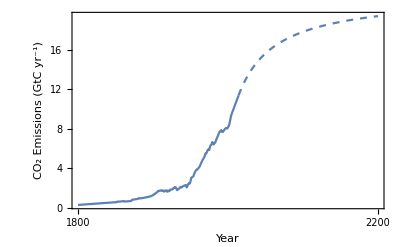

```mathematica
(* saturating energy plot *)
satEmissionPlot=Show[satEmissionPlotPre,satEmissionPlotPost]
```

```mathematica
(*Export["figures/emissionNosocialPlot.png",emissionNosocialPlot,ImageResolution->100];*)
```

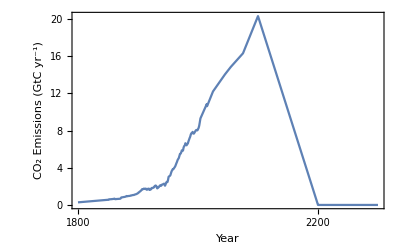

```mathematica
(* lenton emissions plot *)
emissionsLentonPlot=Plot[emissionsLenton[t],{t,0,500},
PlotRange->{All,All},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"CO_2 Emissions (GtC yr^-1)",None},{"Year",None}}]
```

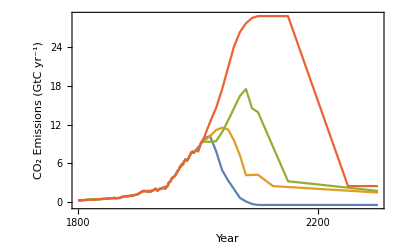

```mathematica
(* rcp emission plots *)
rcpEmissionPlot=Plot[{rcp2p6[t],rcp4p5[t],rcp6[t],rcp8p5[t]},{t,0,500},
PlotRange->{All,All},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"CO_2 Emissions (GtC yr^-1)",None},{"Year",None}}]
```

## Parameters

### Emission Scenario

```mathematica
(* Choose emission scenario from
emissionsLenton, emissionsSoc, rcp2p6, rcp4p6, rcp6, rcp8p5 *)
Clear[emissions]
emissions=emissionsSoc;
```

### Muryshev parameters

```mathematica
f0=2.5*^-2; (* ocean flux constant (2.5-4.5 *10^-2) *)
```

### Social parameters

```mathematica
x0=0.05; (* proportion of mitigators in 2010 *)
κ=0.05;
δ=1;
β=1;
(* response function to temp *)
resType=1; (* 1 sigmoidal, 2 linear *)
fmax=5;
omega=3;
tempThresh=2.5;
noSocial=1; (* 1 if social dynamics are to be included *)


(* temp prediction (linear extrapolation from previous temperatures) *) 
tempProjOnOff=1; (* on 1, off 0 *)
deltatPast=10; (* based on previous number of years *)
deltatFut=25; (* years looking ahead *)
```

### Conversion factors

```mathematica
ka=1.773*^20; (* moles in atmosphere *)
gtcToMol=8.3259*^13;(* factor from gtC to moles *)
gtcToPpm=gtcToMol*10^6/ka; (* factor from gtc to ppmv *)
gtcTogtco2=3.664; (* factor from gtC from gtCO2 *)
secondstoyrs=60*60*24*365; (* factor from seconds to years *)
```

### Initial conditions (pre-industrial)

```mathematica
cat0=596; (* initial carbon in the atmostphere *)
coc0=1.5*^5; (* initial carbon in the ocean *)
cve0=550; (* initial carbon in veg *)
cso0=1500; (*initical carbon in soil *)
temp0=288.15; (* inital temp *)
```

### Lenton parameters

```mathematica
kp=0.184; (* photosyn rate *)
kr=0.092; (*plant respiration rate *)
kt=0.092; (* turnover rate *)
ksr=0.0337; (* soil respiration rate *)
kc=29*^-6; (* compensation point *)
kM=120*^-6; (* half-saturation point - set to 145 for ocean warming *)
```

```mathematica
ea=54.83*^3; (* plant respiration activation energy (Jmol^-1) *)
kMM=1.478; (* photosyn normalising constnat - set to 1.578 for ocean warming *)
kA=8.7039*^9; (* plant respiration normalising constant &*)
kB=157.072; (* soil respiration normalising constant*)
solar=1368; (* solar flux *)
albedo=0.225; (* surface albedo *)
tauch4=0.0231; (* methane opacity *)
p0=1.4*^11; (* water vapour saturation constant *)
(* humidity parameter is fit to give pre-industrial steady state temperature of T=288.15K as in Lenton00 *)
cap=4.69*^23; (* specific heat capacity *)
rgas=8.314; (* universal gas constant *)
rho=1027; (* density of sea water *)
lheat=43655; (* latent heat per mole of water *)
σ=5.67*^-8; (* Stefan-Boltzman constant*)
gtcToMol=8.3259*^13; (* factor to go from gtc to moles *)
aE=5.101*^14; (* earth SA *)
```

### Plot Parameters

```mathematica
(* time ticks *)
timeTicks=Table[{200(i-1),1800+200(i-1)},{i,1,10}];
```

## Functional Forms

### Ocean

```mathematica
(* characteristic c02 solubility in seawater *)
(* lower characteristic solubility, higher temp anomaly *)
Clear[chi]
chi[temp_]:=0.3;
```

```mathematica
(* buffer factor *)
(* higher buffer reduces the total carbon storage of the ocean thus makes equilibrium temperature higher. Global anomaly not affected too much *)
Clear[zeta]
zeta[temp_,cat_]:=60;
```

```mathematica
(* carbon flux to ocean from atmosphere *)
Clear[foc]
foc[temp_,cat_,coc_]:=f0*chi[temp]*(cat-zeta[temp,cat]*cat0*coc/coc0)
```

### Land

```mathematica
(* atmospheric mixing ratio of co2 in atmosphere *)
Clear[pco2a]
pco2a[cat_]:=(cat+cat0)*gtcToMol/ka
```

```mathematica
(* photosynthesis - from Lenton *)
Clear[photo]
photo[cat_,temp_]:=If[pco2a[cat]>kc&& -15<temp<25,
kp*cve0*kMM*((pco2a[cat]-kc)/(kM+pco2a[cat]-kc))*(((15+temp)^2)*(25-temp)/5625),
0];
```

```mathematica
(* respiration of plants *)
Clear[respp]
respp[temp_,cve_]:=kr*(cve+cve0)*kA*Exp[-(ea/(rgas*(temp+temp0)))]
```

```mathematica
(* turnover of plants *)
Clear[turnover]
turnover[cve_]:=kt*(cve+cve0)
```

```mathematica
(* respiration of soil *)
Clear[resps]
resps[temp_,cso_]:=ksr*(cso+cso0)*kB*Exp[-(308.56/(temp+temp0-227.13))]
```

```mathematica
(* carbon flux to land from atmosphere *)
Clear[fla]
fla[cat_,cve_,cso_,temp_]:=photo[cat,temp]-respp[temp,cve]-resps[temp,cso];
```

### Atmosphere

```mathematica
(* opacity of co2 *)
Clear[tauco2]
tauco2[ca_]:=1.73*pco2a[ca]^0.263;
```

```mathematica
(* opacity of h20 *)
Clear[hum]
Clear[tauh2o]
tauh2o[temp_,hum_]:=0.0126*(hum*p0*Exp[-lheat/(rgas*(temp+temp0))])^0.503
```

```mathematica
(* total opacity *)
Clear[tau]
tau[ca_,temp_,hum_]:=tauco2[ca]+tauh2o[temp,hum]+tauch4
```

```mathematica
(* downward flux of radiation *)
Clear[fd]
fd[ca_,temp_,hum_]:=((1-albedo)*solar/4)*(1+3tau[ca,temp,hum]/4)
```

```mathematica
(* Calibrate hum so that equilibirum temperature of 288.15K in 1800 *)
hum=hum/.Quiet[Solve[fd[0,0,hum]-σ temp0^4==0,hum]][[1]]
```

0.591475

### Social - cost of global warming

#### Beckage equivalents

```mathematica
(*(* social response to temperature function *)
Clear[resLin,resLog,resCub,res]
resLin[temp_]:=b1 temp + c1;
resLog[temp_]:=b2/(1+c2 Exp[-d2 temp])-fmax;
resCub[temp_]:=(temp/b3)^3+c3;
Which[resType==1,res[temp_]:=resLin[temp],
resType==2,res[temp_]:=resLog[temp],
resType==3,res[temp_]:=resCub[temp]]*)
```

```mathematica
(*(* Make plot of three functions *)
warmCostPlot=Plot[{resLin[temp],resLog[temp],resCub[temp]},{temp,-tempMax,tempMax},
LabelStyle->14,
AxesLabel->{"T","f(T)"},
PlotLegends->Placed[{"Linear","Logistic","Cubic"},Scaled[{0.2,0.8}]]]*)
```

```mathematica
(*Export["figures/temp_response.pdf",warmCostPlot];*)
```

#### Sigmoidal (fermi-dirac)

```mathematica
Clear[resSig,resLin]
resSig[temp_]:=fmax/(1+Exp[-omega(temp-tempThresh)]);
resLin[temp_]:=fmax/5*temp;
```

```mathematica
(* assign response function *)
Clear[res]
Which[resType==1,res[temp_]:=resSig[temp],
resType==2,res[temp_]:=resLin[temp]];
```

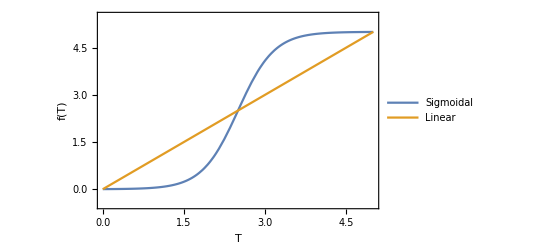

```mathematica
tempResponsePlot=Plot[{resSig[temp],resLin[temp]},{temp,0,5},
LabelStyle->14,
Frame->True,
FrameLabel->{{"f(T)",""},{"T",""}},
PlotRange->{{0,5},{-0.5,fmax+0.5}},
PlotLegends->Placed[LineLegend[TMBcolours[[1;;2]],{"Sigmoidal","Linear"},LabelStyle->12],Scaled[{0.2,0.8}]]]
```

```mathematica
Export["figures/tempResponsePlot.png",tempResponsePlot,ImageResolution->100];
```

```mathematica
emissionsLenton
```

InterpolatingFunction[{{0., 1200.}}, <>]

```mathematica
rcp2p6
```

InterpolatingFunction[{{0., 500.}}, <>]

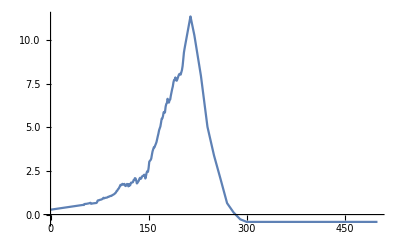

```mathematica
Plot[%8489[x],{x,0.,500.}]
```

## Dynamic Equations

```mathematica
tmax=800;
```

```mathematica
(* Clear variable names *)
Clear[cat,coc,cve,cso,temp,soc]
```

```mathematica
(* run simulation *)
sim=NDSolve[{cat'[t]==emissions[t](1-soc[t])/(1-x0)-foc[temp[t],cat[t],coc[t]]-fla[cat[t],cve[t],cso[t],temp[t]],
coc'[t]==foc[temp[t],cat[t],coc[t]],
cve'[t]==photo[cat[t],temp[t]]-respp[temp[t],cve[t]]-turnover[cve[t]],
cso'[t]==turnover[cve[t]]-resps[temp[t],cso[t]],
temp'[t]==secondstoyrs*(aE/cap)*(fd[cat[t],temp[t],hum]-σ (temp[t]+temp0)^4),
soc'[t]==Which[noSocial==0,0,
0≤t≤214,0,
t>214 && tempProjOnOff==1,κ*soc[t]*(1-soc[t])*(-β+res[temp[t]+(deltatFut/deltatPast)*(temp[t]-temp[t-deltatPast])]+(δ*(2soc[t]-1))),
t>214 && tempProjOnOff==0,κ*soc[t]*(1-soc[t])*(-β+res[temp[t]]+(δ*(2soc[t]-1)))],
cat[t/;t≤0]==0,
coc[t/;t≤0]==0,
cve[t/;t≤0]==0,
cso[t/;t≤0]==0,
temp[t/;t≤0]==0,
soc[t/;t≤0]==x0},
{cat,coc,cve,cso,temp,soc},
{t,0,tmax}];
```

```mathematica
(* obtain series functions *)
Clear[catSeries,cocSeries,cveSeries,csoSeries,tempSeries,socSeries,emissionSeries]
catSeries[t_]:=cat[t]/.sim[[1]]
cocSeries[t_]:=coc[t]/.sim[[1]]
cveSeries[t_]:=cve[t]/.sim[[1]]
csoSeries[t_]:=cso[t]/.sim[[1]]
tempSeries[t_]:=temp[t]/.sim[[1]]
socSeries[t_]:=soc[t]/.sim[[1]]
emissionSeries[t_]:=emissions[t]*(1-socSeries[t])
```

```mathematica
(* x axis plot range *)
plRange={100,800};
```

```mathematica
(* emissions *)
emissionSocialPlot=Plot[emissions[t](1-socSeries[t])/(1-x0),{t,0,800},
PlotRange->{plRange,{0,20}},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"CO_2emissions (gtC yr^-1)",None},{"Year",None}}];
```

```mathematica
(* social behaviour *)
socPlot=Plot[socSeries[t]/.sim,{t,0,tmax},
PlotRange->{plRange,All},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"Proportion mitigators",None},{"Year",None}}];
```

```mathematica
(* carbon in atmosphere in ppmv *)
catPlot2=Plot[(catSeries[t]+cat0)*gtcToPpm/.sim,{t,0,tmax},
PlotRange->{plRange,{0,1200}},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"Atmospheric CO_2 (ppmv)",None},{"Year",None}}];
```

```mathematica
(* temperature change *)
tempPlot=Plot[tempSeries[t],{t,0,tmax},
PlotRange->{plRange,{0,6}},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"Temperature change (K)",None},{"Year",None}}];
```

```mathematica
(* carbon in the ocean *)
(*cocPlot=Plot[cocSeries[t]*gtcToPpm,{t,0,tmax},
PlotRange->{plRange,All},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"Oceanic CO_2 (ppmv)",None},{"Year",None}}];*)
```

```mathematica
(* carbon in vegetation *)
(*cvePlot=Plot[cveSeries[t]*gtcToPpm,{t,0,tmax},
PlotRange->{plRange,All},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"Vegetation CO_2 (ppmv)",None},{"Year",None}}];*)
```

```mathematica
(* carbon in the soil *)
(*csoPlot=Plot[csoSeries[t]*gtcToPpm,{t,0,tmax},
PlotRange->{plRange,All},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"Soil CO_2 (ppmv)",None},{"Year",None}}];*)
```

### Plots of fluxes from atmosphere to ocean / land

```mathematica
legend=LineLegend[{TMBcolours[[1]],TMBcolours[[2]]},{"ocean","land"}]
```

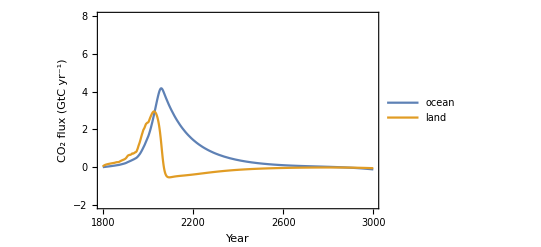

```mathematica
fluxPlot=Plot[{foc[tempSeries[t],catSeries[t],cocSeries[t]],fla[catSeries[t],cveSeries[t],csoSeries[t],tempSeries[t]]},{t,0,1200},
PlotRange->{All,{-2,8}},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
PlotLegends->Placed[legend,Scaled[{0.8,0.5}]],
FrameLabel->{{"CO_2 flux (GtC yr^-1)",None},{"Year",None}}]
```

### Plot Grid

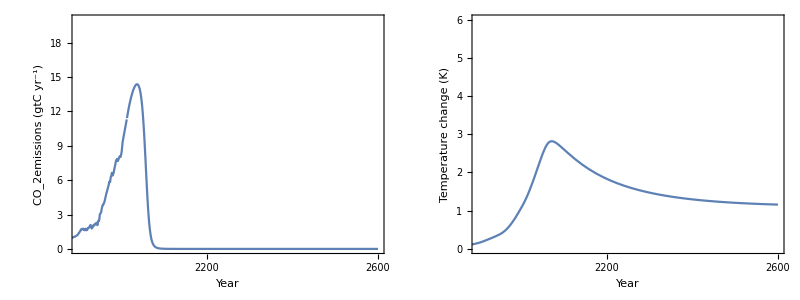

```mathematica
tempEmissionPlot=Grid[{{emissionSocialPlot,tempPlot}}]
```

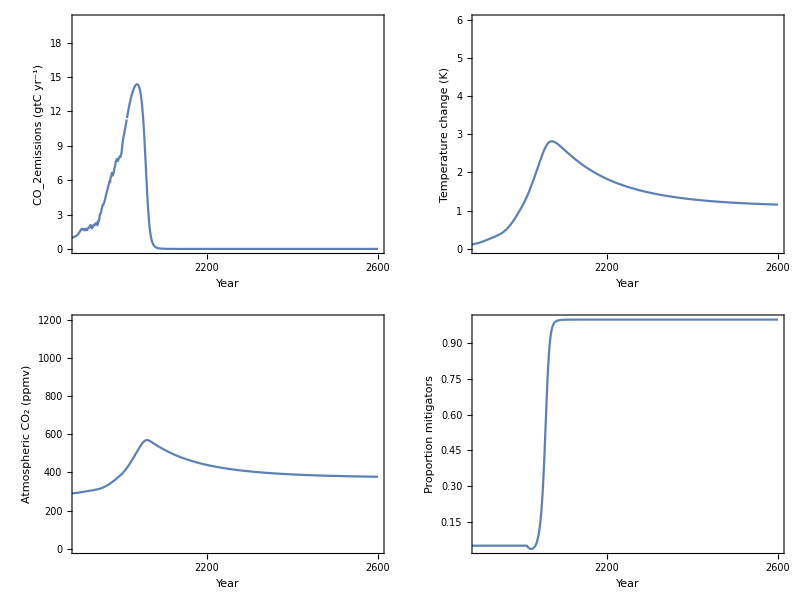

```mathematica
gridPlot=Grid[{{emissionSocialPlot,tempPlot},{catPlot2,socPlot}}]
```

```mathematica
lentonEquivPlot=Grid[{{emissionSocialPlot,tempPlot},{catPlot2,fluxPlot}}];
```

## Export Data

```mathematica
(*seriesData={Flatten[Table[emissionSeries[t],{t,0,1200,1}]],Flatten[Table[tempSeries[t],{t,0,1200,1}]],Flatten[Table[catSeries[t],{t,0,1200,1}]],Flatten[Table[socSeries[t],{t,0,1200,1}]]};*)
```

```mathematica
(*Export["export_data/series_data/sim_tempProj_100.dat",seriesData];*)
```